0.966667

{}

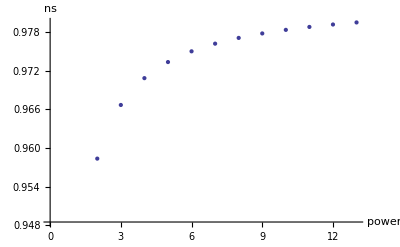

```mathematica
(* This Notebook plots the spectral index ns as a function of monomial  power for potentials of the form v=λ*ϕ^p. The slow roll approximation is used to find ns and the number of efolds nsr. ns is evaluated at nsr=60. *)
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
(* Define a potential *)
v[ϕ_] := λ*ϕ^4
findNs := Module[{nsr,ϕ60,ns},
(* Define number of efolds using slow-roll approx *)
nsr[ϕ_] := v[ϕ]/v''[ϕ];
(* find ϕ60, ϕ at n=60 *)
ϕ60 = NSolve[nsr[ϕ]==60,ϕ];
(* Find ns in the slow roll approx as a function of ϕ *)
ns[ϕ_] := 1-v'[ϕ]^2/v[ϕ]^2+2/v[ϕ]*(v''[ϕ]-v'[ϕ]^2/v[ϕ]);
(* Find the spectral tilt at ϕ60 *)
Last[ns[ϕ]/.ϕ60 ]]
v[ϕ_] := λ*ϕ^4 
findNs
(*v[ϕ_] := 1+Log[ϕ]
findNs
v[ϕ_] := λ*Exp[-α*ϕ]
findNs
v[ϕ_] := 1+Cos[ϕ]
findNs*)
NsList = {}
For[p=2,p<15,p++,
v[ϕ_] := λ*ϕ^p;
AppendTo[NsList,findNs]] (* Append returns a new list. AppendTo appends to given list. *)
ListPlot[NsList,AxesLabel->{power,ns}]
```